## For the sum of two uniforms

```mathematica
a=TransformedDistribution[0.5u+0.5v,{u\[Distributed]UniformDistribution[{0,300}],v\[Distributed] UniformDistribution[{0,300}]}];
```

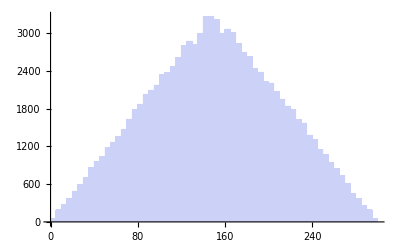

```mathematica
Histogram[RandomVariate[a,{100000}]]
```

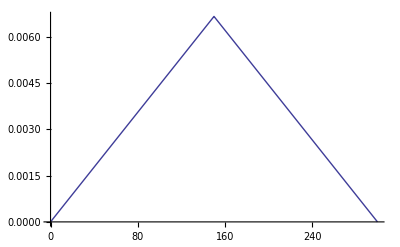

```mathematica
Plot[PDF[a,x],{x,0,300}]
```

## For the sum of three uniforms

```mathematica
aPDF[n_,x_] := PDF[UniformSumDistribution[n,{0,300/n}],x]
aDist[n_] := UniformSumDistribution[n,{0,300/n}];
aStndDev[n_]:= StandardDeviation[aDist[n]]
```

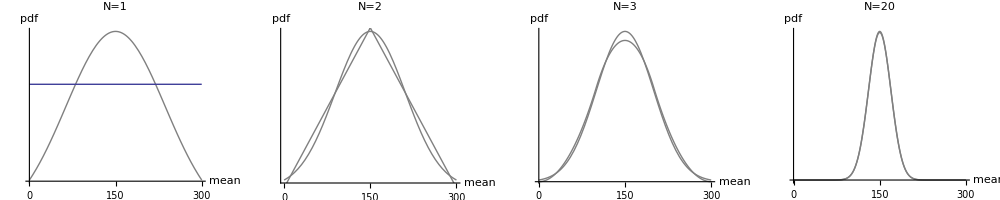

```mathematica
g1=Show[Plot[PDF[NormalDistribution[150,aStndDev[1]],x],{x,0,300},PlotRange->{Full,Full},Ticks->{All,None},PlotStyle->Gray,AxesLabel->{mean,pdf},PlotLabel->"N=1"],ListLinePlot[Table[{x,aPDF[1,x]},{x,0,300,0.1}]]];
g2=Show[Plot[PDF[NormalDistribution[150,aStndDev[2]],x],{x,0,300},PlotRange->{Full,Full},Ticks->{All,None},PlotStyle->Gray,AxesLabel->{mean,pdf},PlotLabel->"N=2"],ListLinePlot[Table[{x,aPDF[2,x]},{x,0,300,0.1}],Ticks->{All,None},PlotStyle->Gray,AxesLabel->{mean,pdf}]];
g3=Show[Plot[PDF[NormalDistribution[150,aStndDev[3]],x],{x,0,300},PlotRange->{Full,Full},Ticks->{All,None},PlotStyle->Gray,AxesLabel->{mean,pdf},PlotLabel->"N=3"],ListLinePlot[Table[{x,aPDF[3,x]},{x,0,300,0.1}],Ticks->{All,None},PlotStyle->Gray,AxesLabel->{mean,pdf}]];
g10=Show[Plot[PDF[NormalDistribution[150,aStndDev[20]],x],{x,0,300},PlotRange->{Full,Full},Ticks->{All,None},PlotStyle->Gray,AxesLabel->{mean,pdf},PlotLabel->"N=20"],ListLinePlot[Table[{x,aPDF[20,x]},{x,0,300,0.1}],Ticks->{All,None},PlotStyle->Gray,AxesLabel->{mean,pdf}]];

Show[GraphicsRow[{g1,g2,g3,g10}],ImageSize->1000]
```